# Práctica 1

## Ejercicio 1

```mathematica
N[(4-6^(1/3))/(1+Log[10,3]),11]
```

1.4777929707

## Ejercicio 2

```mathematica
l1=Range[1,200,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

```mathematica
Length[l1]
```

100

```mathematica
l2=Log[l1]//N
```

{0.,1.09861,1.60944,1.94591,2.19722,2.3979,2.56495,2.70805,2.83321,2.94444,3.04452,3.13549,3.21888,3.29584,3.3673,3.43399,3.49651,3.55535,3.61092,3.66356,3.71357,3.7612,3.80666,3.85015,3.89182,3.93183,3.97029,4.00733,4.04305,4.07754,4.11087,4.14313,4.17439,4.20469,4.23411,4.26268,4.29046,4.31749,4.34381,4.36945,4.39445,4.41884,4.44265,4.46591,4.48864,4.51086,4.5326,4.55388,4.57471,4.59512,4.61512,4.63473,4.65396,4.67283,4.69135,4.70953,4.72739,4.74493,4.76217,4.77912,4.79579,4.81218,4.82831,4.84419,4.85981,4.8752,4.89035,4.90527,4.91998,4.93447,4.94876,4.96284,4.97673,4.99043,5.00395,5.01728,5.03044,5.04343,5.05625,5.0689,5.0814,5.09375,5.10595,5.11799,5.1299,5.14166,5.15329,5.16479,5.17615,5.18739,5.1985,5.20949,5.22036,5.23111,5.24175,5.25227,5.26269,5.273,5.2832,5.2933}

```mathematica
l2[[20]]
```

3.66356

### Sugerencia

```mathematica
t=Table[Log[2i-1],{i,100}]
t[[20]]//N
```

{0,Log[3],Log[5],Log[7],Log[9],Log[11],Log[13],Log[15],Log[17],Log[19],Log[21],Log[23],Log[25],Log[27],Log[29],Log[31],Log[33],Log[35],Log[37],Log[39],Log[41],Log[43],Log[45],Log[47],Log[49],Log[51],Log[53],Log[55],Log[57],Log[59],Log[61],Log[63],Log[65],Log[67],Log[69],Log[71],Log[73],Log[75],Log[77],Log[79],Log[81],Log[83],Log[85],Log[87],Log[89],Log[91],Log[93],Log[95],Log[97],Log[99],Log[101],Log[103],Log[105],Log[107],Log[109],Log[111],Log[113],Log[115],Log[117],Log[119],Log[121],Log[123],Log[125],Log[127],Log[129],Log[131],Log[133],Log[135],Log[137],Log[139],Log[141],Log[143],Log[145],Log[147],Log[149],Log[151],Log[153],Log[155],Log[157],Log[159],Log[161],Log[163],Log[165],Log[167],Log[169],Log[171],Log[173],Log[175],Log[177],Log[179],Log[181],Log[183],Log[185],Log[187],Log[189],Log[191],Log[193],Log[195],Log[197],Log[199]}

3.66356

## Ejercicio 3

### ERROR AL DEFINIR LA FUNCIÓN F (X)

```mathematica
f[x_]=(Sin[x+2]*Log[x])/((e^x)-2)(*ESTÁ MAL DEFINIDA*)
```

(Log[x] Sin[2+x])/(-2+e^x)

#### FORMA CORRECTA

```mathematica
f[x_]=(Sin[x+2]*Log[x])/(Exp[x]-2)
```

(Log[x] Sin[2+x])/(-2+ⅇ^x)

```mathematica
g[x_,y_]=(x^2-Pi)/Sqrt[x-y]
```

(-π+x^2)/(√(x-y))

```mathematica
f[Pi]
```

-(Log[π] Sin[2])/(-2+e^π)

```mathematica
CORRECCIÓN
```

```mathematica
f[Pi]
```

-(Log[π] Sin[2])/(-2+ⅇ^π)

```mathematica
f[Pi]//N (*NO CALCULA LA APROXIMACIÓN NUMÉRICA POR ESTAR MAL DEFINIDA LA EXPONENCIAL*)
```

-1.0409/(-2.+e^3.14159)

```mathematica
f[Pi]//N (*CORREGIDO*)
```

-0.0492368

```mathematica
g[6,2]
```

(36-π)/2

```mathematica
g[6.,2.]
```

16.4292

## Ejercicio 4

```mathematica
h[x_]=2^x
```

2^x

```mathematica
j[x_]=(1-x)/x
```

(1-x)/x

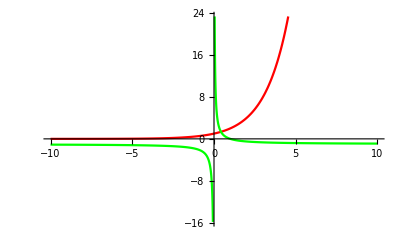

```mathematica
Plot[{h[x],j[x]},{x,-10,10},PlotStyle->{Red,Green}]
```